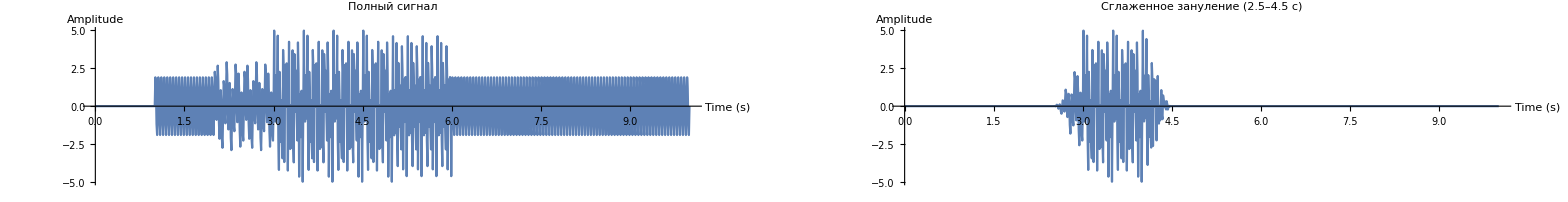

```mathematica
spec=<|MaxTime->10,SampleRate->100,Components->{<|Amplitude->2,Frequency->20,TStart->1,TEnd->10|>,<|Amplitude->3,Frequency->32,TStart->3,TEnd->6|>,<|Amplitude->1,Frequency->6,TStart->2,TEnd->5|>}|>;


data=Table[{t,Total@Map[If[#[TStart]<=t<=#[TEnd],1,0]*#[Amplitude]*Sin[2 Pi t #[Frequency]]&,spec[Components]]},{t,0,spec[MaxTime],1/spec[SampleRate]}];

(*Функция сглаживающего окна*)
smoothMask[t_,tStart_,tEnd_,edge_]:=Module[{rampUp,rampDown},rampUp=0.5*(1+Cos[Pi*(tStart+edge-t)/edge]);
rampDown=0.5*(1+Cos[Pi*(t-tEnd+edge)/edge]);
Which[t<=tStart,0,t<tStart+edge,rampUp,t<=tEnd-edge,1,t<=tEnd,rampDown,True,0]];


cut=<|Start->2.5,End->4.5|>;
edge=0.5;(*сглаживание по 0.5 с на краях*)smoothMaskedData=Map[{#[[1]],smoothMask[#[[1]],cut[Start],cut[End],edge]*#[[2]]}&,data];

(* ===6. Построение графиков===*)
p1=ListLinePlot[data,PlotRange->All,PlotLabel->"Полный сигнал",AspectRatio->1/5,ImageSize->1000,AxesLabel->{"Time (s)","Amplitude"}];

p2=ListLinePlot[smoothMaskedData,PlotRange->All,PlotLabel->"Сглаженное зануление (2.5–4.5 с)",AspectRatio->1/5,ImageSize->1000,AxesLabel->{"Time (s)","Amplitude"}];

GraphicsRow[{p1,p2}]
```